```mathematica
(* Narrowband pulses with fixed profile bandwidths ϵ = 0.9, 0.8, 0.7, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/3 *)
(* Error < 10^-4 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootNB;
err=0.0001;
error=", error="<>ToString@err;
totalArea[rule_,sym_]:=Module[
{vars=rule/.Rule[a_,b_]->a},
area=Total[Abs[vars[[Length[vars]/2+1;;-1]]/.rule]];
If[sym,area=2area-vars[[-1]]/.rule];
area]
```

```mathematica
(*N=3 -- Inefficient*)
```

NB4; p=1, error=0.0001

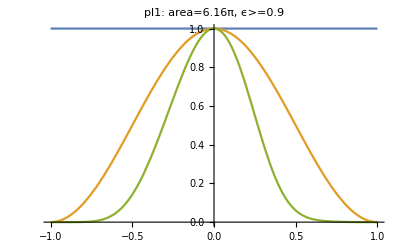

NB4; p=1/2, error=0.0001

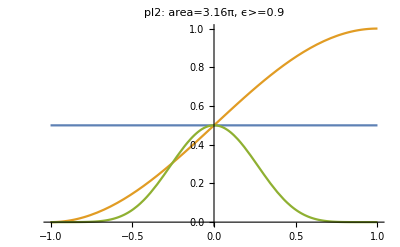

NB4; p=1/3, error=0.0001

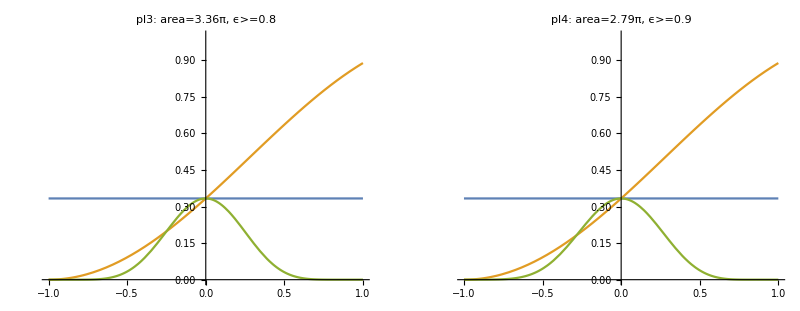

```mathematica
(*N=4*)
sequence=U[Δ4,Ω4].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,False]]

pl1=plt[1,{Δ1->2.3469,Δ2->-1.4247,Δ3->0.9857,Δ4->1.5999,Ω1->1.8053,Ω2->1.5477,Ω3->0.112,Ω4->2.7},"pl1"];

pl2=plt[1/2,{Δ1->0.4886,Δ2->0.9461,Δ3->-0.35,Δ4->0.281,Ω1->1.5917,Ω2->0.,Ω3->0.6816,Ω4->0.883},"pl2"];

pl3=plt[1/3,{Δ1->-0.3091,Δ2->-1.144,Δ3->2.3546,Δ4->-0.1503,Ω1->1.2658,Ω2->0.3523,Ω3->0.7356,Ω4->1.0088},"pl3"];
pl4=plt[1/3,{Δ1->0.3252,Δ2->1.0535,Δ3->-0.319,Δ4->0.2308,Ω1->1.3332,Ω2->0.1433,Ω3->0.3258,Ω4->0.986},"pl4"];

GGrid[Text[Style["NB4; p=1"<>error,FontSize->20]],{{pl1,Null,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/2"<>error,FontSize->20]],{{pl2,Null,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB4; p=1/3"<>error,FontSize->20]],{{pl3,pl4,Null,Null}},ImageSize->Full]
```

NB5; p=1

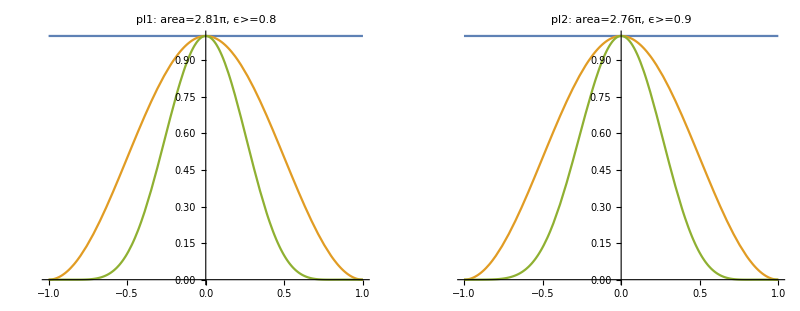

NB5; p=1/2

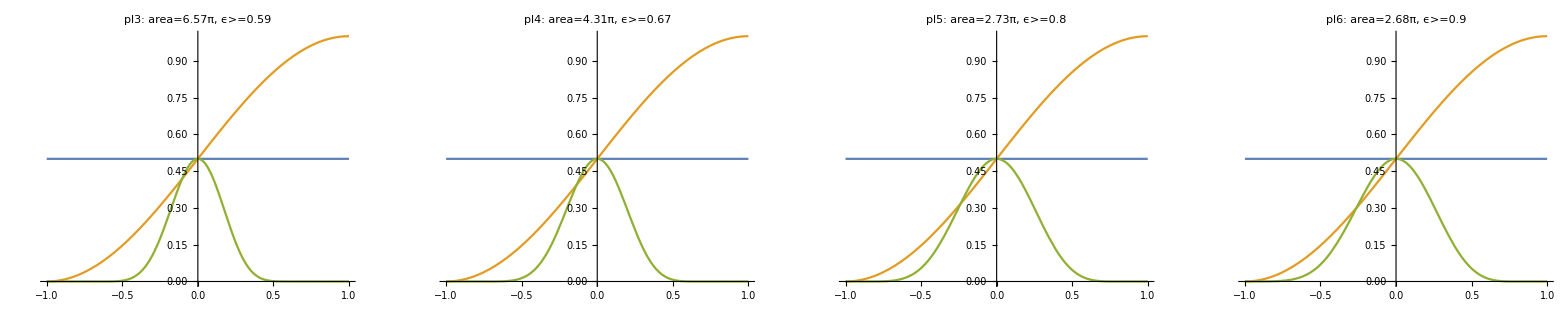

NB5; p=1/3

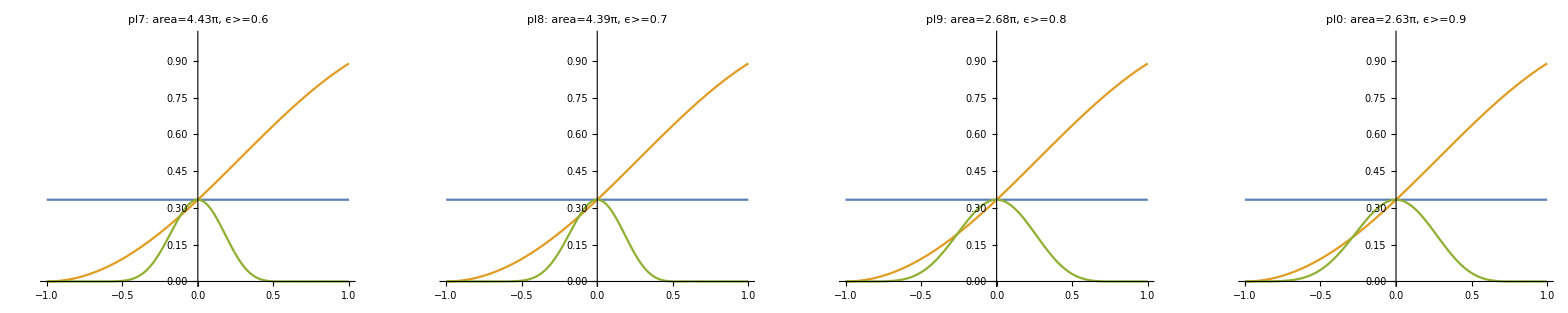

```mathematica
(*N=5*)
sequence=U[Δ1,Ω1].U[Δ2,Ω2].U[Δ3,Ω3].U[Δ2,Ω2].U[Δ1,Ω1];
plt[p_,rule_,label_]:=plot[p,err,sequence,rule,0,label, totalArea[rule,True]]

pl1=plt[1.0,{Δ1->0.6864,Δ2->-0.1434,Δ3->1.12,Ω1->0.4324,Ω2->0.4795,Ω3->0.9829},"pl1"];
pl2=plt[1.0,{Δ1->0.6835,Δ2->-0.1439,Δ3->1.1556,Ω1->0.4329,Ω2->0.4635,Ω3->0.9655},"pl2"];

pl3=plt[0.5,{Δ1->2.6869,Δ2->1.6164,Δ3->3.3584,Ω1->0.7924,Ω2->1.9728,Ω3->1.0419},"pl3"];
pl4=plt[0.5,{Δ1->0.8202,Δ2->-0.593,Δ3->1.6004,Ω1->0.4203,Ω2->1.293,Ω3->0.8789},"pl4"];
pl5=plt[0.5,{Δ1->0.6076,Δ2->-0.3383,Δ3->1.3352,Ω1->0.4311,Ω2->0.5315,Ω3->0.809},"pl5"];
pl6=plt[0.5,{Δ1->0.8422,Δ2->-0.0402,Δ3->1.1397,Ω1->0.4254,Ω2->0.3056,Ω3->1.216},"pl6"];

pl7=plt[1/3,{Δ1->0.8037,Δ2->-0.5294,Δ3->1.5144,Ω1->0.4338,Ω2->1.3259,Ω3->0.9143},"pl7"];
pl8=plt[1/3,{Δ1->0.7978,Δ2->-0.5329,Δ3->1.5199,Ω1->0.4304,Ω2->1.3158,Ω3->0.8972},"pl8"];
pl9=plt[1/3,{Δ1->-0.7726,Δ2->0.4879,Δ3->0.7204,Ω1->0.4341,Ω2->0.6919,Ω3->0.433},"pl9"];
pl0=plt[1/3,{Δ1->0.7708,Δ2->-0.4079,Δ3->-0.883,Ω1->0.4158,Ω2->0.6223,Ω3->0.5533},"pl0"];

GGrid[Text[Style["NB5; p=1",FontSize->20]],{{pl1,pl2,Null,Null}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/2",FontSize->20]],{{pl3,pl4,pl5,pl6}},ImageSize->Full]
GGrid[Text[Style["NB5; p=1/3",FontSize->20]],{{pl7,pl8,pl9,pl0}},ImageSize->Full]
```